# Physics 234 PS #10 / Part B (25) Code Evaluation on Chapter 3 of CSM

Ziyang Gao
4/30/2018

## Section 1: What is the problem about

Read the following three sections in Chapter 3 in CSM: Introduction, 3.1 (The Diffusion-Limited Aggregation Model), and 3.2 (Visualizing Diffusion-Limited Aggregation). Then, work through the code in these sections in your own notebook. 
	Your notebook should contain all the code and appropriate output, along with comments on any of the code you didn’t understand or that did not work correctly. In the last section of your notebook, include all new functions and structures (ones we have not discussed in class) that were used or mentioned in the sections.

## Section 2: Code piece and code check

```mathematica
DLA[s_Integer,n_Integer]:=
Module[{loc,rad,particleCount=0,stepChoices={{1,0},{0,1},{-1,0},{0,-1}}},

occupiedSites={{0,0}};
While[Length[occupiedSites]<n,
++particleCount;
rad=Max[Abs[occupiedSites]]+s;
loc=FixedPoint[
(#+stepChoices[[Random[Integer,{1,4}]]])&,
  Round[rad{Cos[#],Sin[#]}]&[Random[Real,{0,N[2 Pi]}]],
SameTest->(Apply[Plus,#2^2]>(rad+s)^2||
Intersection[occupiedSites,Map[Function[y,y+#2],stepChoices]]≠{}&)];
If[Apply[Plus,loc^2]<rad^2,
occupiedSites=Join[occupiedSites,{loc}]]];
Print["The number of particles released was",particleCount];
occupiedSites]
```

```mathematica
agg=DLA[10,30];
```

The number of particles released was105

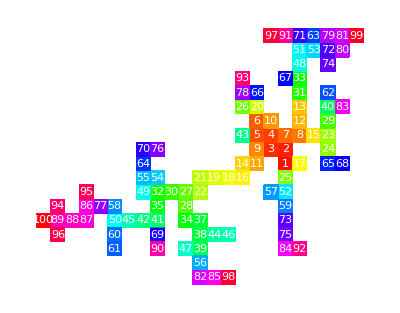

```mathematica
ShowDLA[sites_]:=Module[{structures,s=Length[sites]},
structures={};
Map[(AppendTo[structures,{Hue[.99#/s],Rectangle[sites[[#]]-{0.5,0.5},sites[[#]]+{0.5,0.5}],RGBColor[1,1,1],Text[#,sites[[#]]]}])&,Range[s]];
Show[Graphics[structures],Axes->None,AspectRatio->Automatic,PlotRange->All]
]
ShowDLA[agg]
```

The original code can’t show the graph properly, so I deleted “opts_” and all the opts in the code to help it come out.

The number of particles released was4605

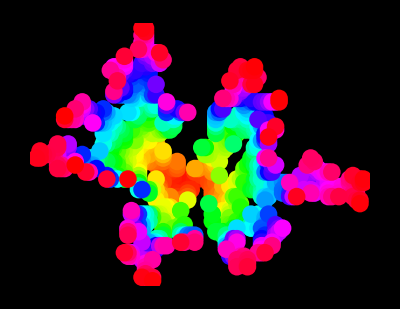

```mathematica
ShowDLA2[sites_,opts_Rule]:=
Module[{len=Length[sites],points,colors},
points=Map[Point,sites];
colors=Map[Hue,Range[len]/len];
Show[Graphics[{PointSize[1/Sqrt[len]],Transpose[{colors,points}]},opts,Axes->None,AspectRatio->Automatic,PlotRange->All]]
]
agg=DLA[2,1000];
ShowDLA2[agg,Background->GrayLevel[0]]
```

## Section 3 : Comments and questions

I don’t quite understand line “Round[rad{Cos[#],Sin[#]}]&[Random[Real,{0,N[2 Pi]}]]”. But given that this line generates a site nearest to a random point on the peripheral of the circle centered (0,0) with a radius max absolute coordinate value in occupiedSites plus s, I could guess that the Cos and Sin probably helps generate a location on the circle. 
	I also don’t understand how does the part of “Map[Function[y,y+#2]” work in line “Intersection[occupiedSites,Map[Function[y,y+#2],stepChoices]]≠{}&)];”. Because I feel like the Map of Function should use subtraction instead of plus. It should look like Map[Function[y,y-#2], so that the difference gradually shrinks to zero.
	I don’t see how DLA and showDLA is connected/related. Does showDLA simulate the same aggregation process as the non-graphical DLA? Also, just quickly going through the build-in graphics commands in class would be helpful.

## Section 4 : New functions and structures

1. FixedPoints[ f,expr]: starts with expr, then applies f repeatedly until the result no longer changes.
2. Round[rad {Cos[#], Sin[#]}] &[Random[Real, {0, N[2 Pi]}]]: generates a nearest neighbor of a peripheral point on a circle.
3. SameTest -> ( ): Apply the same testing method each time, for example, the f in FixedPoints is called.
4. Graphics[{PointSize[1/Sqrt[len]],Transpose[{colors,points}]}]: create a graph , specify point size and match colors with the points.